```mathematica
numberOfAgents = 10;
donationCost = -10;
buyCost = -40;
donationHealthChange=3;
usageUtil = 5;
waitCost = -1;
fullToolHealth=10;

agentParams = Array[Function[x,
{(*RandomReal[0.4], (* How often a tool is needed *)*)
0.4,
RandomReal[0.0], (* Prob to buy tool *)
RandomReal[0.001], (* Prob to donate *)
0, (* Has tool (tool health) *)
0
}],numberOfAgents];
```

```mathematica
(* Returns the utility, the updated agent, and change in poolHealth.
int, agent, int *)
CalculatePayoff[agent_,nPTools_]:=Module[
{p=agent[[1]],pb=agent[[2]],
pd=agent[[3]],toolHealth=agent[[4]],
util=agent[[5]],poolHealthChange=0},
If[RandomReal[]<p,
If[toolHealth>0,
util+=usageUtil; toolHealth-=1,
If[RandomReal[]<pb,
toolHealth=fullToolHealth;
util+=buyCost+usageUtil,
If[nPTools>0,
util+=usageUtil;poolHealthChange-=1,
util+=waitCost]
]
],
If[RandomReal[]<pd,
poolHealthChange+=donationHealthChange;
util+=donationCost,
util+=0
]
];
{{p,pb,pd,toolHealth,util},poolHealthChange}
];

CalculatePayoff[{0,0,1,5,0},3]
```

{{0,0,1,5,-10},3}

```mathematica
MutateValue[v_] := Module[{value},
If[v>0.5,distance = 1-v,distance =v];
value=RandomVariate[NormalDistribution[v,(distance/4)+0.1]];
If[value<=0,0,Min[value,1]]
];
MutateValue[0.5]
```

0.668594

{-6,5,-28,-15,-26,-3,-20,-19,-32,-20}

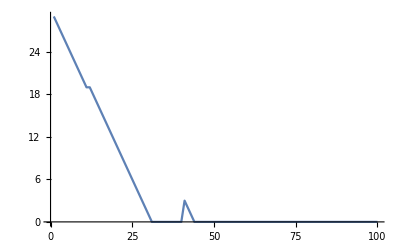

```mathematica
DoRound[agentList_,initPoolHealth_,iterations_]:=Module[
{poolHealth=initPoolHealth,
agents=agentList,
agentPayoffs=ConstantArray[0,Length[agentList]],
PHhistory = {}},
For[i=0,i<iterations,i++,
nPoolTools=poolHealth/fullToolHealth;
agents=RandomSample[agents];
For[j=1,j<Length[agents],j++,
{newAgent, healthChange}=CalculatePayoff[agents[[j]],nPoolTools];
agents[[j]]=newAgent;
poolHealth+=healthChange;
nPoolTools=If[healthChange==-1,healthChange,nPoolTools];
];
PHhistory = Append[PHhistory,poolHealth];
];
{agents, PHhistory}
];

{ag, hp} =DoRound[agentParams,30,100];
Map[Last,ag]
ListLinePlot[hp]
```